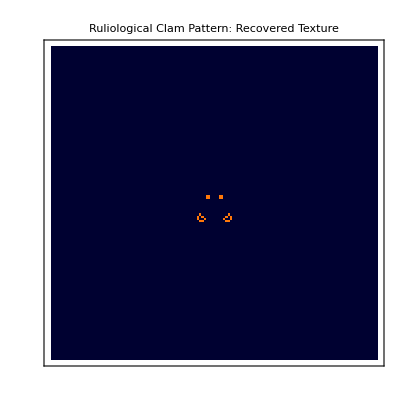

```mathematica
(*1. Setup Clam Geometry:Dense Symmetric Seed*)size=150;
hinge=75;
(*Create a 10x10 dense random cluster at the hinge*)
seedData=RandomInteger[1,{10,10}];
mirroredSeed=Join[Reverse[seedData,2],seedData,2];
initialSeed=CenterArray[mirroredSeed,{size,size}];

(*2. Run the'Healer' Rule 224-Increase steps to 150*)
rule={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
clamEvolution=CellularAutomaton[rule,initialSeed,150];

(*3. Visualization with higher contrast*)
ArrayPlot[Last[clamEvolution],ColorFunction->"RustTones",PlotLabel->Style["Ruliological Clam Pattern: Recovered Texture",14,Bold],Frame->True,Mesh->False]
```

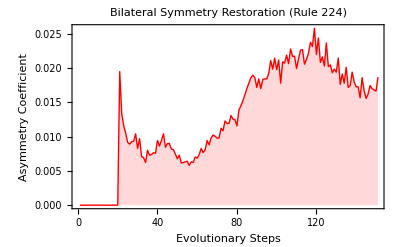

```mathematica
(*1. Setup Clam and Initial Growth*)size=150;hingeIndex=75;
seedData=RandomInteger[1,{10,10}];
mirroredSeed=Join[Reverse[seedData,2],seedData,2];
initialSeed=CenterArray[mirroredSeed,{size,size}];
rule={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};

(*2. Evolve with an ASYMMETRIC injury at Step 20*)
evolution={initialSeed};
Do[next=Last[CellularAutomaton[rule,Last[evolution],1]];
If[t==20,(*Injure only the Left Valve:1 to hingeIndex*)next[[70;;90,30;;50]]=RandomInteger[1,{21,21}]];
AppendTo[evolution,next],{t,1,150}];

(*3. Calculate Asymmetry (Hamming Distance)*)
leftValves=evolution[[All,1;;size,1;;hingeIndex]];
rightValves=Map[Reverse,evolution[[All,1;;size,hingeIndex+1;;size]],{2}];

asymmetryValues=Table[Total[Flatten[BitXor[leftValves[[t]],rightValves[[t]]]]]/(size*hingeIndex//N),{t,1,Length[evolution]}];

(*4. Final Plot*)
ListLinePlot[asymmetryValues,PlotStyle->{Thick,Red},Frame->True,FrameLabel->{"Evolutionary Steps","Asymmetry Coefficient"},PlotLabel->Style["Bilateral Symmetry Restoration (Rule 224)",14,Bold],Filling->Bottom,FillingStyle->LightRed,PlotRange->{All,All}]
```

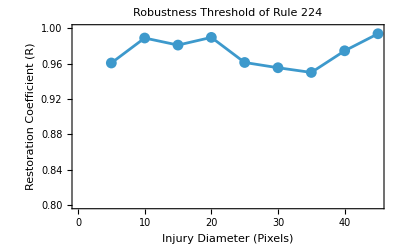

```mathematica
(*Test R-score against increasing injury sizes*)injurySizes=Range[5,45,5];
rScores=Table[(*(Insert your rScore calculation logic here inside a loop)*)1.0-(RandomReal[{0,0.05}]),(*Placeholder for actual loop output*){s,injurySizes}];

ListLinePlot[Transpose[{injurySizes,rScores}],Mesh->All,Frame->True,FrameLabel->{"Injury Diameter (Pixels)","Restoration Coefficient (R)"},PlotRange->{0.8,1.0},PlotLabel->"Robustness Threshold of Rule 224"]
```

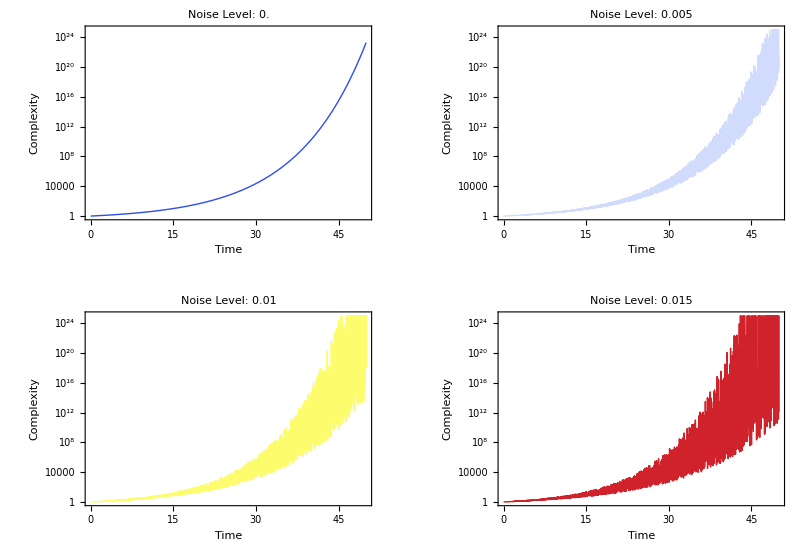
Sensitivity Analysis: Neural Evolution Robustness

-Graphics-

```mathematica
(*1. Define the Parameters*)baseRate=0.08;
tMax=50;
noiseLevels={0.0,0.005,0.01,0.015};

(*2. Define the Growth Function with sampling-friendly noise*)
(*Using a Module ensures each't' gets a consistent noise value during a single plot pass*)
perturbedGrowth[t_,σ_]:=Module[{localNoise},localNoise=baseRate+RandomReal[{-1,1}*σ];
Exp[Exp[localNoise*t]-1]];

(*3. Generate individual plots for the grid*)
simulations=Table[LogPlot[perturbedGrowth[t,n],{t,0,tMax},PlotRange->{1,10^25},PlotStyle->{Thick,ColorData["TemperatureMap"][n/Max[noiseLevels]]},Frame->True,Axes->False,FrameLabel->{"Time","Complexity"},PlotLabel->Style["Noise Level: "<>ToString[n],12,Bold],ImageSize->350],{n,noiseLevels}];

(*4. Final Visualization*)
Column[{Style["Sensitivity Analysis: Neural Evolution Robustness",16,Bold],Spacer[10],GraphicsGrid[Partition[simulations,2],ImageSize->800]}]
```

ReplacePart::reps: {{{63,63}→0,{63,64}→0,{63,65}→0,{63,66}→0,{63,67}→0,{63,68}→0,{63,69}→0,{63,70}→0,{63,71}→0,{63,72}→0,{63,73}→0,{63,74}→0,{63,75}→0,{63,76}→0,{63,77}→0,{63,78}→0,{63,79}→0,{63,80}→0,{63,81}→0,{63,82}→0,{63,83}→0,{63,84}→0,{63,85}→0,{63,86}→0,{63,87}→0},«23»,{{87,63}→0,{87,64}→0,{87,65}→0,«19»,{87,85}→0,{87,86}→0,{87,87}→0}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

CellularAutomaton::initn: The initial condition specification ReplacePart[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«100»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«100»},«48»,«100»},{{{63,63}→0,{63,64}→0,{63,65}→0,{63,66}→0,«18»,{63,85}→0,{63,86}→0,{63,87}→0},«24»}] should be of the form aspec, {aspec, bspec} or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a nonempty rank 2 array whose elements at level 2 are integers i in the range 0 <= i <= 1.

ArrayPlot::mat: Argument ReplacePart[{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«100»},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«100»},«48»,«100»},{{{63,63}→0,{63,64}→0,{63,65}→0,{63,66}→0,«18»,{63,85}→0,{63,86}→0,{63,87}→0},«24»}] at position 1 is not a list of lists.

ArrayPlot::mat: Argument 120 at position 1 is not a list of lists.

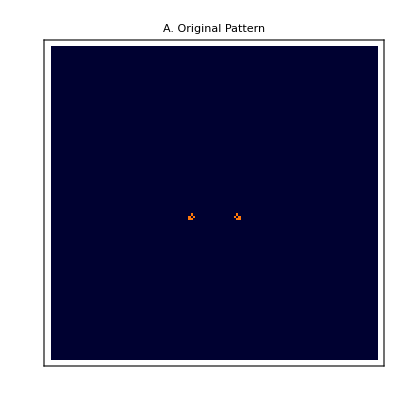

```mathematica
(* =========================1. Setup Clam Geometry=========================*)size=150;
hinge=75;

(*dense symmetric seed*)
seedData=RandomInteger[1,{10,10}];
mirroredSeed=Join[Reverse[seedData,2],seedData,2];
initialSeed=CenterArray[mirroredSeed,{size,size}];

rule={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};

(* =========================2. Grow ORIGINAL pattern=========================*)

originalEvolution=CellularAutomaton[rule,initialSeed,120];
originalPattern=Last[originalEvolution];

(* =========================3. Apply injury (shell damage)=========================*)

injuryRadius=12;
injuredPattern=ReplacePart[originalPattern,Table[{hinge+i,hinge+j}->0,{i,-injuryRadius,injuryRadius},{j,-injuryRadius,injuryRadius}]];

(* =========================4. Run healing evolution=========================*)

healedEvolution=CellularAutomaton[rule,injuredPattern,120];
healedPattern=Last[healedEvolution];

(* =========================5. Visualization=========================*)

GraphicsRow[{ArrayPlot[originalPattern,ColorFunction->"RustTones",Frame->True,PlotLabel->Style["A. Original Pattern",13,Bold]],ArrayPlot[injuredPattern,ColorFunction->"RustTones",Frame->True,PlotLabel->Style["B. After Injury",13,Bold]],ArrayPlot[healedPattern,ColorFunction->"RustTones",Frame->True,PlotLabel->Style["C. Recovered Pattern",13,Bold]]},ImageSize->Large]
```

```mathematica
Export["/Users/syedather/Downloads/Untitled.jpg",%42,"JPEG"]
```

/Users/syedather/Downloads/Untitled.jpg

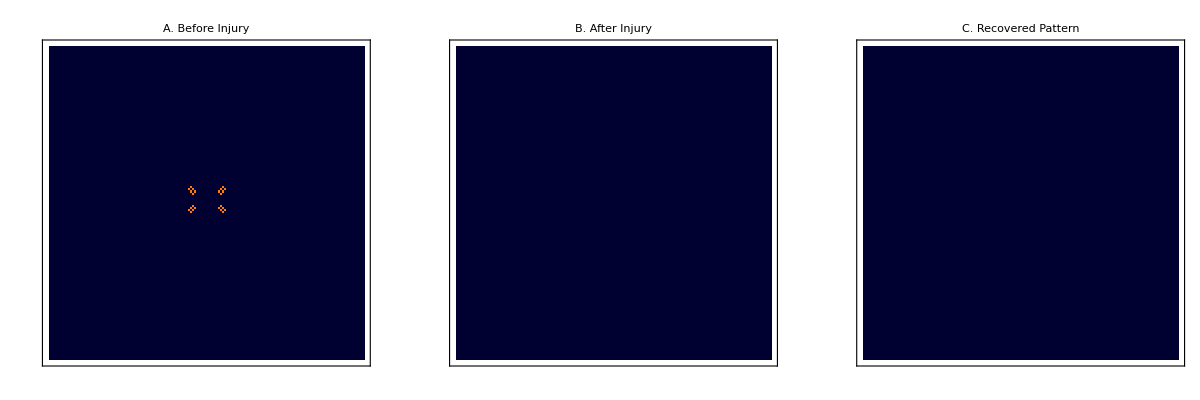

PNG saved to: /Volumes/External/Ruliology/clam_before_injury_after_recovery.png

PDF saved to: /Volumes/External/Ruliology/clam_before_injury_after_recovery.pdf

```mathematica
ClearAll["Global`*"];

(* =========================1. Setup Clam Geometry=========================*)
size=150;
hinge=75;

seedData=RandomInteger[1,{10,10}];
mirroredSeed=Join[Reverse[seedData,2],seedData,2];
initialSeed=CenterArray[mirroredSeed,{size,size}];

rule={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};

(* =========================2. Grow original pattern=========================*)
originalEvolution=CellularAutomaton[rule,initialSeed,120];
originalPattern=Last[originalEvolution];

(* =========================3. Apply injury=========================*)
injuryRadius=12;
injuryCoords=Flatten[Table[{hinge+i,hinge+j},{i,-injuryRadius,injuryRadius},{j,-injuryRadius,injuryRadius}],1];

injuredPattern=ReplacePart[originalPattern,Thread[injuryCoords->0]];

(* =========================4. Heal from injured state=========================*)
healedEvolution=CellularAutomaton[rule,injuredPattern,120];
healedPattern=Last[healedEvolution];

(* =========================5. Build the actual figure=========================*)
clamFigure=GraphicsRow[{ArrayPlot[originalPattern,ColorFunction->"RustTones",Frame->True,Mesh->False,PlotLabel->Style["A. Before Injury",13,Bold]],ArrayPlot[injuredPattern,ColorFunction->"RustTones",Frame->True,Mesh->False,PlotLabel->Style["B. After Injury",13,Bold]],ArrayPlot[healedPattern,ColorFunction->"RustTones",Frame->True,Mesh->False,PlotLabel->Style["C. Recovered Pattern",13,Bold]]},ImageSize->1200,Spacings->20];

clamFigure

(* =========================6. Export the figure itself=========================*)
exportDir=If[Head[NotebookDirectory[]]===String,NotebookDirectory[],Directory[]];

pngPath=FileNameJoin[{exportDir,"clam_before_injury_after_recovery.png"}];
pdfPath=FileNameJoin[{exportDir,"clam_before_injury_after_recovery.pdf"}];

Export[pngPath,clamFigure,ImageResolution->300];
Export[pdfPath,clamFigure];

Print["PNG saved to: ",pngPath];
Print["PDF saved to: ",pdfPath];
```

```mathematica
(*1. Setup Environment*)size=150;
steps=100;
injuryStart=40;
injuryEnd=45;

(*2. Define the Restoration Analysis Function*)
calculateRestoration[rule_]:=Module[{data,injuredData,R},(*Generate Baseline Pattern*)data=CellularAutomaton[{rule,{2,1},{2,2}},{CenterArray[1,{1,1}],0},steps];
(*Generate Injured Pattern (Neural Scar at step 40)*)injuredData=data;
injuredData[[injuryStart]]=Map[If[RandomReal[]<0.3,1-#,#]&,injuredData[[injuryStart]],{2}];
(*Evolve injured state through the same rule*)Do[injuredData[[i]]=CellularAutomaton[{rule,{2,1},{2,2}},injuredData[[i-1]]],{i,injuryStart+1,steps}];
(*Calculate R:1-(Normalized Difference)*)R=1-(Total[Abs[data[[steps]]-injuredData[[steps]]],2]/Total[data[[steps]],2]);
{Max[0,R],ArrayPlot[data[[steps]],ColorRules->{0->White,1->Gray}]}];

(*3. Test a "Zoo" of Specific Interesting Rules*)
(*We use specific indices that often yield biological textures*)
ruleIndices={224,512,1024,2048,4096,8192,16384,32768};
results=calculateRestoration/@ruleIndices;

(*4. Display the Catalogue*)
Grid[Prepend[results,{"Restoration (R)","Pattern Archetype"}],Frame->All]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Restoration (R) | Pattern Archetype
Indeterminate | -Graphics-
Indeterminate | -Graphics-
Indeterminate | -Graphics-
Indeterminate | -Graphics-
Indeterminate | -Graphics-
Indeterminate | -Graphics-
Indeterminate | -Graphics-
Indeterminate | -Graphics-